## Dynamic Season Rankings (The “Global” Model)

1. Show runtime for each code block.

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

2. Import season data.

```mathematica
data = Import["/Users/totam/Downloads/ModCombinedYearsRankingSpread.csv"];
```

3. For predictions, remove outliers; we consider an outlier to be a difference between the point spread and the realized spread that exceeds 14 points AND has a difference in predicted winners.

```mathematica
editeddata = Select[data, Abs[#[[12]]-#[[13]]]<=14 || ((#[[12]] >=0 && #[[13]] >= 0)|| (#[[12]] <= 0 && #[[13]] <= 0))&];
```

rank[data_, week_, grad_, resid_, diff_]:
	data_: Array of game results (season, week, team identification, score differential, etc.); note that columns have to align with columns given in data
	week_: Last week used to rank teams (the week here is the TOTAL week of the data, not the week of a single season)
	grad_: Boolean to return the gradient of ranking (TRUE for gradient of Massey ranking, FALSE otherwise)
	resid_: Boolean to return  the residual of the ranking (TRUE for residual of Massey ranking, FALSE otherwise)
	diff_: Boolean to return  the weighted point differentials (TRUE for point differentials, FALSE otherwise)
Returns array of rankings

```mathematica
rank[data_, week_, grad_, resid_, diff_] := 
Module[{i, numgames, year, yearlength, originaldiff, differential, games, multiplier, new, season, playoffs,diagonal, newdiff, rankings, teamnames, weektested,years, teamnum, adjusted, final, weightdifferential, winteam, loseteam, finalresidual},(

numgames = Length[Select[data[[All,3]],#<=week &]];
year = data[[numgames, 1]];
yearlength = Length[Select[data[[All,1]],#==year&]];
originaldiff = data[[(numgames-yearlength+1);;numgames, 12]];
differential = Array[0 &, {yearlength, 1}];
games = Array[0 &, {yearlength, 32}];

For[i = numgames-yearlength+1, i<= numgames, i++, 
multiplier = 1;
If[data[[i,1]]!=year,multiplier = 0.9];
If[data[[i,7]]=="@",differential[[i-numgames+yearlength]] =multiplier^(data[[numgames, 3]]-data[[i, 3]])*(Min[9, originaldiff[[i-numgames+yearlength]]]) ,
  differential[[i-numgames+yearlength]] = multiplier^(data[[numgames, 3]]-data[[i, 3]])*(Min[9, originaldiff[[i-numgames+yearlength]]]) 
];
games[[i-numgames+yearlength, data[[i, 6]]]] = 1; 
games[[i-numgames+yearlength, data[[i, 9]]]] = -1
];

new=Transpose[games].games;
new[[32, All]] = 1;

season = 1;
playoffs = 3;
diagonal = DiagonalMatrix[Array[season &, yearlength]];
For[i = 1, i<= yearlength, i++, 
If[data[[numgames-yearlength+i,2]] == 1, diagonal[[i, i]] = playoffs];
];
newdiff = Transpose[games].diagonal.differential;
newdiff[[32]] = 0;

rankings = LinearSolve[new, newdiff]*1.0;
teamnames = {"Arizona Cardinals","Atlanta Falcons","Baltimore Ravens","Buffalo Bills","Carolina Panthers","Chicago Bears","Cincinnati Bengals","Cleveland Browns","Dallas Cowboys","Denver Broncos","Detroit Lions","Green Bay Packers","Houston Texans","Indianapolis Colts","Jacksonville Jaguars","Kansas City Chiefs","Miami Dolphins","Minnesota Vikings","New England Patriots","New Orleans Saints","New York Giants","New York Jets","Las Vegas Raiders","Philadelphia Eagles","Pittsburgh Steelers","Los Angeles Rams","Los Angeles Chargers","San Francisco 49ers","Seattle Seahawks","Tampa Bay Buccaneers","Tennessee Titans","Washington Commanders"};
weektested = Array[data[[numgames, 4]]&, 32];
years = Array[year &, 32];
teamnum = Range[32];

If[grad == TRUE,
weightdifferential = diagonal.differential;
winteam = data[[(numgames-yearlength+1);;numgames, 6]];
loseteam = data[[(numgames-yearlength+1);;numgames, 9]];
finalresidual = List[];
For[i = 1, i<=yearlength, i++,
finalresidual = Append[finalresidual, (rankings[[winteam[[i]]]]-rankings[[loseteam[[i]]]])];
];
Return[finalresidual];
];

If[resid == TRUE,
weightdifferential = diagonal.differential;
winteam = data[[(numgames-yearlength+1);;numgames, 6]];
loseteam = data[[(numgames-yearlength+1);;numgames, 9]];
finalresidual = List[];
For[i = 1, i<=yearlength, i++,
finalresidual = Append[finalresidual, weightdifferential[[i]]-(rankings[[winteam[[i]]]]-rankings[[loseteam[[i]]]])];
];
Return[finalresidual];
];

If[diff == TRUE,
Return[diagonal.differential];
];

rankings = rankings*10/(Max[rankings]-Min[rankings]);

adjusted = rankings-Min[rankings];
adjusted = adjusted/Max[adjusted];
final = Transpose[List[years, weektested, teamnum, teamnames, rankings, adjusted]];

final = ReverseSortBy[final, Last];
Return[final];)]
```

4. Calculate weekly (modified) Massey rankings from the 2013 - 2023 seasons. Note that we include the last week of the 2012 season for predictive purposes.

```mathematica
result = List[];
Module[{week},
For[week = 21, week <= 255, week++,
result = Join[result, rank[data, week, FALSE, FALSE, FALSE]];
]
]
Export["/Users/totam/Downloads/NewMassey.csv", result];
```

## Implementing HodgeRank

graphgen[data_, week_, weighted_, directed_]:
	data_: Array of game results (season, week, team identification, score differential, etc.); note that columns have to align with columns given in data
	week_: Last week used to rank teams (the week here is the TOTAL week of the data, not the week of a single season)
	weighted_: Boolean to assign weights to graph edges (TRUE for weight assignment, FALSE otherwise)
	directed_: Boolean to return directed graph (TRUE for directed graph, FALSE otherwise)
Returns graph representation of a years worth of games up to week_

```mathematica
graphgen[data_, week_, weighted_, directed_] :=
Module[{i, numgames, year, yearlength, originaldiff, differential, games, home, multiplier, season, playoffs, newdiff, weight, rankings, weektested,years, adjusted},(
numgames = Length[Select[data[[All,3]],#<=week &]];
year = data[[numgames, 1]];
yearlength = Length[Select[data[[All,1]],#==year&]];
originaldiff = data[[(numgames-yearlength+1);;numgames, 12]];
differential = Array[0 &, {yearlength, 1}];
games = List[];
weight = List[];
season = 1;
playoffs = 3;

For[i = numgames-yearlength+1, i<= numgames, i++, 
multiplier = 1;
If[data[[i,1]]!=year,multiplier = 0.9];
If[data[[i,7]]=="@",differential[[i-numgames+yearlength]] =multiplier^(data[[numgames, 3]]-data[[i, 3]])*(Min[9, originaldiff[[i-numgames+yearlength]]]) ,
  differential[[i-numgames+yearlength]] = multiplier^(data[[numgames, 3]]-data[[i, 3]])*(Min[9, originaldiff[[i-numgames+yearlength]]]) 
];
If[data[[i,2]]==1,
weight = Append[weight,playoffs*differential[[i-numgames+yearlength]]], weight = Append[weight, season*differential[[i-numgames+yearlength]]]
];
If[directed == FALSE,
If[data[[i,6]] < data[[i,9]],games = Append[games,data[[i,6]]<->data[[i,9]]],games = Append[games,data[[i,9]]<->data[[i,6]]]]
];
If[directed == TRUE, games = Append[games,data[[i,6]]->data[[i,9]]]]
];
Return[games];

If[directed == FALSE && weighted == FALSE, Return[Graph[games]]];
Return[Graph[games, EdgeWeight -> weight, VertexLabels->Automatic]];
)]
```

5. We walk through a step-by-step process of HodgeRank. First, generate undirected and directed graph representations of a given week (stored as testingweek). Record the edge lists of the directed and undirected graphs.

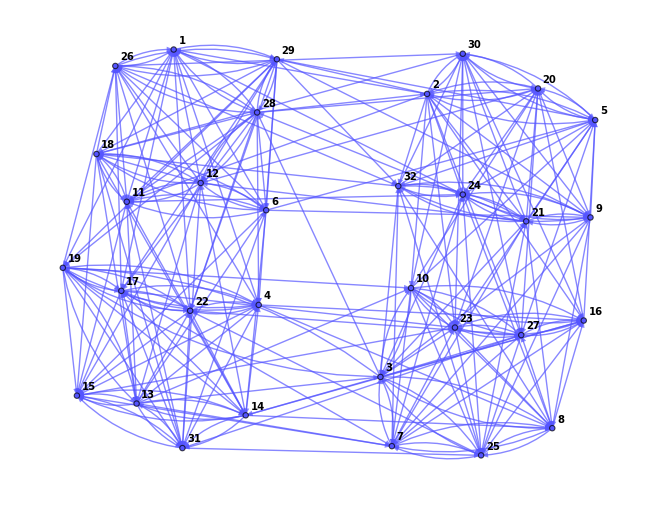

```mathematica
testingweek = 21;
gradient = rank[data, testingweek, grad = TRUE, FALSE, FALSE];
residual = rank[data, testingweek, FALSE, resid = TRUE, FALSE];
actualdifferential = rank[data, testingweek, FALSE, FALSE, diff = TRUE];
directed = Graph[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32},graphgen[data, testingweek,TRUE, TRUE], VertexLabels->{Automatic}, VertexLabelStyle->Directive[Black,Bold,10],VertexStyle -> Lighter[Blue], VertexSize -> Small, EdgeStyle -> {Lighter[Blue]}, EdgeShapeFunction->{{"CarvedArrow", "ArrowSize" -> 0.025}}]
undirected = graphgen[data, testingweek, FALSE, FALSE];
WeightedAdjacencyMatrix[directed]//MatrixForm;
graphlaplacian = KirchhoffMatrix[directed];
direcEdge = EdgeList[directed];
undirecEdge = EdgeList[undirected];
Export["/Users/totam/Downloads/nfl2012endgraph.jpg",directed, ImageResolution -> 1200];
```

6. Recall the graph Helmholtzian (see https://doi.org/10.1137/18M1223101 ) is the sum of two matrices. We calculate the first matrix here, which we call conjugateLaplacian (since it is constructed using the conjugate of the components used to construct the graph Laplacian).

```mathematica
subLaplacian = Array[0&,{Length[direcEdge],32}];
Module[{i},
For[i = 1, i<=Length[direcEdge],i++,
subLaplacian[[i,direcEdge[[i,1]]]]=-1;
subLaplacian[[i,direcEdge[[i,2]]]]=1;
];
]
subLaplacian //MatrixForm;
conjugateLaplacian = subLaplacian.Transpose[subLaplacian];
Dimensions[conjugateLaplacian]
```

{267,267}

7. Identify unique edges (that is, unique pairwise games between two teams) to properly identify triangle subgraphs.

```mathematica
uniqueUndirec = List[];
Module[{i,j,isIn},
For[i = 1, i<=Length[undirecEdge],i++,
isIn = FALSE;
For[j = 1, j<=Length[uniqueUndirec],j++,
If[undirecEdge[[i]]==uniqueUndirec[[j]],isIn = TRUE];
If[undirecEdge[[i,1]]==uniqueUndirec[[j,2]]&&undirecEdge[[i,2]]==uniqueUndirec[[j,1]],isIn = TRUE];
];
If[isIn == FALSE, uniqueUndirec = Append[uniqueUndirec, undirecEdge[[i]]]];
]
]
Length[uniqueUndirec]
```

214

8. Use Mathematica’s built-in FindCycle function to determine unique triangle subgraphs of undirected graph. Record the number of cycles on the directed graph in ending.

```mathematica
cycle = DeleteDuplicates[FindCycle[uniqueUndirec,{3},All]];
ending = 0;
Module[{i, j,first, second, third, firstdone, seconddone, thirddone, firstweight, secondweight, thirdweight, len},
For[i = 1, i<=Length[cycle], i++, 
first = cycle[[i,1]];
second = cycle[[i,2]];
third = cycle[[i,3]];
firstdone = List[];
seconddone = List[];
thirddone = List[];
firstweight = List[];
secondweight = List[];
thirdweight = List[];
For[j = 1, j<=Length[direcEdge],j++,
If[direcEdge[[j,1]]==first[[1]] && direcEdge[[j,2]]==first[[2]],
firstdone = Append[firstdone,j]; firstweight = Append[firstweight , 1],
If[direcEdge[[j,1]]==first[[2]]&&direcEdge[[j,2]]==first[[1]], firstdone = Append[firstdone,j]; firstweight = Append[firstweight, -1]]
];
If[direcEdge[[j,1]]==second[[1]]&&direcEdge[[j,2]]==second[[2]],
seconddone = Append[seconddone, j]; secondweight = Append[secondweight, 1],
If[direcEdge[[j,1]]==second[[2]]&&direcEdge[[j,2]]==second[[1]],seconddone = Append[seconddone,j]; secondweight = Append[secondweight, -1]]
];
If[direcEdge[[j,1]]==third[[1]]&&direcEdge[[j,2]]==third[[2]],
thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, 1],
If[direcEdge[[j,1]]==third[[2]]&&direcEdge[[j,2]]==third[[1]],thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, -1]]
];
];
len = Length[firstdone]*Length[seconddone]*Length[thirddone];
ending = ending + len;
];
]
ending
```

1156

9. Iterate through  possible cycles on the undirected graph to identify all possible cycles. Calculate directionality of triangle flows and store directional weights in triangles. Note that triangles is used to compute the second matrix of the graph Helmholtzian composition.

```mathematica
triangles = Array[0 &, {ending, Length[undirecEdge]}];
traversed = List[];
wherestop = 0;
Module[{i, j, k, l, m, n, first, second, third, firstdone, seconddone, thirddone, firstweight, secondweight, thirdweight, listthem, listweight, len},
For[i = 1, i<=Length[cycle], i++, 
first = cycle[[i,1]];
second = cycle[[i,2]];
third = cycle[[i,3]];
firstdone = List[];
seconddone = List[];
thirddone = List[];
firstweight = List[];
secondweight = List[];
thirdweight = List[];
For[j = 1, j<=Length[direcEdge],j++,
If[direcEdge[[j,1]]==first[[1]] && direcEdge[[j,2]]==first[[2]],
firstdone = Append[firstdone,j]; firstweight = Append[firstweight , 1],
If[direcEdge[[j,1]]==first[[2]]&&direcEdge[[j,2]]==first[[1]], firstdone = Append[firstdone,j]; firstweight = Append[firstweight, -1]]
];
If[direcEdge[[j,1]]==second[[1]]&&direcEdge[[j,2]]==second[[2]],
seconddone = Append[seconddone, j]; secondweight = Append[secondweight, 1],
If[direcEdge[[j,1]]==second[[2]]&&direcEdge[[j,2]]==second[[1]],seconddone = Append[seconddone,j]; secondweight = Append[secondweight, -1]]
];
If[direcEdge[[j,1]]==third[[1]]&&direcEdge[[j,2]]==third[[2]],
thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, 1],
If[direcEdge[[j,1]]==third[[2]]&&direcEdge[[j,2]]==third[[1]],thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, -1]]
];
];
len = Length[firstdone]*Length[seconddone]*Length[thirddone];
listthem = List[];
listweight = List[];
For[k = 1, k<=Length[firstdone],k++,
For[l = 1, l <= Length[seconddone], l++,
For[m = 1, m <= Length[thirddone], m++,
listthem = Append[listthem, {firstdone[[k]], seconddone[[l]], thirddone[[m]]}];
listweight  = Append[listweight, {firstweight[[k]], secondweight[[l]], thirdweight[[m]]}];
];
];
];
For[n = 1, n <= len, n++,
triangles[[wherestop+n, listthem[[n,1]]]] = listweight[[n,1]];
triangles[[wherestop+n,listthem[[n,2]]]] = listweight[[n,2]];
triangles[[wherestop+n,listthem[[n,3]]]]=listweight[[n,3]];
];
wherestop = wherestop + len;
];
]
```

10. Construct the graph Helmholtzian. 
     (a) If the graph Helmholtzian is singular, compute the inverse Helmholtzian as the Moore-Penrose (pseudo) inverse; we explicitly use SVD to compute the pseudoinverse. Then, use the inverse Helmholtzian to compute the harmonic operator in the Helmholtz decomposition.
     (b) If the graph Helmholtzian is non-singular, the harmonic operator in the Helmholtz decomposition is simply zero.
From here, we easily get the harmonic and curl components of the residual decomposition.

```mathematica
graphHelmholtzian = conjugateLaplacian+Transpose[triangles].triangles;
If[Det[graphHelmholtzian] == 0,
inverseHelmholtzian = SingularValueDecomposition[N[graphHelmholtzian]][[3]].PseudoInverse[SingularValueDecomposition[N[graphHelmholtzian], Tolerance -> 0][[2]]].Transpose[SingularValueDecomposition[N[graphHelmholtzian]][[1]]];
identity = IdentityMatrix[Length[graphHelmholtzian]];
harmonicOperator = identity-inverseHelmholtzian.graphHelmholtzian,
harmonicOperator = Array[0 &, {Length[graphHelmholtzian], Length[graphHelmholtzian]}];
];
```

```mathematica
harmonicComponent = harmonicOperator.actualdifferential;
curlComponent = residual-harmonicComponent;
```

getteamnums[data_, week_]:
	data_: Array of game results (season, week, team identification, score differential, etc.); note that columns have to align with columns given in data
	week_: Last week used to rank teams (the week here is the TOTAL week of the data, not the week of a single season)
Returns array of participating teams for games up to week_

```mathematica
getteamnums[data_, week_] := 
Module[{i, numgames, year, yearlength, games},(
numgames = Length[Select[data[[All,3]],#<=week &]];
year = data[[numgames, 1]];
yearlength = Length[Select[data[[All,1]],#==year&]];
games = List[];
For[i = numgames-yearlength+1, i<= numgames, i++, 
games = Append[games, {data[[i,3]], data[[i,6]], data[[i,9]]}];
];
Return[games];)]
```

11. Utilize the complete HodgeRank implementation for the 2013 - 2023 seasons. Record the gradient flows, the residual, and the residual decomposition into the curl and harmonic flows.

```mathematica
hodgeFinal = List[];
Module[{a, b},
For[a = 21, a <= 255, a++,
testingweek = a;
gradient = rank[editeddata, testingweek, grad = TRUE, FALSE, FALSE];
residual = rank[editeddata, testingweek, FALSE, resid = TRUE, FALSE];
actualdifferential = rank[editeddata, testingweek, FALSE, FALSE, diff = TRUE];
directed = graphgen[editeddata, testingweek,TRUE, TRUE];
undirected = graphgen[editeddata, testingweek, FALSE, FALSE];
WeightedAdjacencyMatrix[directed]//MatrixForm;
graphlaplacian = KirchhoffMatrix[directed];
direcEdge = EdgeList[directed];
undirecEdge = EdgeList[undirected];

subLaplacian = Array[0&,{Length[direcEdge],32}];
For[b = 1, b<=Length[direcEdge],b++,
subLaplacian[[b,direcEdge[[b,1]]]]=-1;
subLaplacian[[b,direcEdge[[b,2]]]]=1;
];
subLaplacian //MatrixForm;
conjugateLaplacian = subLaplacian.Transpose[subLaplacian];

uniqueUndirec = List[];
Module[{i,j,isIn},
For[i = 1, i<=Length[undirecEdge],i++,
isIn = FALSE;
For[j = 1, j<=Length[uniqueUndirec],j++,
If[undirecEdge[[i]]==uniqueUndirec[[j]],isIn = TRUE];
If[undirecEdge[[i,1]]==uniqueUndirec[[j,2]]&&undirecEdge[[i,2]]==uniqueUndirec[[j,1]],isIn = TRUE];
];
If[isIn == FALSE, uniqueUndirec = Append[uniqueUndirec, undirecEdge[[i]]]];
]
];

cycle = DeleteDuplicates[FindCycle[uniqueUndirec,{3},All]];
ending = 0;
Module[{i, j,first, second, third, firstdone, seconddone, thirddone, firstweight, secondweight, thirdweight, len},
For[i = 1, i<=Length[cycle], i++, 
first = cycle[[i,1]];
second = cycle[[i,2]];
third = cycle[[i,3]];
firstdone = List[];
seconddone = List[];
thirddone = List[];
firstweight = List[];
secondweight = List[];
thirdweight = List[];
For[j = 1, j<=Length[direcEdge],j++,
If[direcEdge[[j,1]]==first[[1]] && direcEdge[[j,2]]==first[[2]],
firstdone = Append[firstdone,j]; firstweight = Append[firstweight , 1],
If[direcEdge[[j,1]]==first[[2]]&&direcEdge[[j,2]]==first[[1]], firstdone = Append[firstdone,j]; firstweight = Append[firstweight, -1]]
];
If[direcEdge[[j,1]]==second[[1]]&&direcEdge[[j,2]]==second[[2]],
seconddone = Append[seconddone, j]; secondweight = Append[secondweight, 1],
If[direcEdge[[j,1]]==second[[2]]&&direcEdge[[j,2]]==second[[1]],seconddone = Append[seconddone,j]; secondweight = Append[secondweight, -1]]
];
If[direcEdge[[j,1]]==third[[1]]&&direcEdge[[j,2]]==third[[2]],
thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, 1],
If[direcEdge[[j,1]]==third[[2]]&&direcEdge[[j,2]]==third[[1]],thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, -1]]
];
];
len = Length[firstdone]*Length[seconddone]*Length[thirddone];
ending = ending + len;
];
];

triangles = Array[0 &, {ending, Length[undirecEdge]}];
traversed = List[];
wherestop = 0;
Module[{i, j, k, l, m, n, first, second, third, firstdone, seconddone, thirddone, firstweight, secondweight, thirdweight, listthem, listweight, len},
For[i = 1, i<=Length[cycle], i++, 
first = cycle[[i,1]];
second = cycle[[i,2]];
third = cycle[[i,3]];
firstdone = List[];
seconddone = List[];
thirddone = List[];
firstweight = List[];
secondweight = List[];
thirdweight = List[];
For[j = 1, j<=Length[direcEdge],j++,
If[direcEdge[[j,1]]==first[[1]] && direcEdge[[j,2]]==first[[2]],
firstdone = Append[firstdone,j]; firstweight = Append[firstweight , 1],
If[direcEdge[[j,1]]==first[[2]]&&direcEdge[[j,2]]==first[[1]], firstdone = Append[firstdone,j]; firstweight = Append[firstweight, -1]]
];
If[direcEdge[[j,1]]==second[[1]]&&direcEdge[[j,2]]==second[[2]],
seconddone = Append[seconddone, j]; secondweight = Append[secondweight, 1],
If[direcEdge[[j,1]]==second[[2]]&&direcEdge[[j,2]]==second[[1]],seconddone = Append[seconddone,j]; secondweight = Append[secondweight, -1]]
];
If[direcEdge[[j,1]]==third[[1]]&&direcEdge[[j,2]]==third[[2]],
thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, 1],
If[direcEdge[[j,1]]==third[[2]]&&direcEdge[[j,2]]==third[[1]],thirddone = Append[thirddone,j]; thirdweight = Append[thirdweight, -1]]
];
];
len = Length[firstdone]*Length[seconddone]*Length[thirddone];
listthem = List[];
listweight = List[];
For[k = 1, k<=Length[firstdone],k++,
For[l = 1, l <= Length[seconddone], l++,
For[m = 1, m <= Length[thirddone], m++,
listthem = Append[listthem, {firstdone[[k]], seconddone[[l]], thirddone[[m]]}];
listweight  = Append[listweight, {firstweight[[k]], secondweight[[l]], thirdweight[[m]]}];
];
];
];
For[n = 1, n <= len, n++,
triangles[[wherestop+n, listthem[[n,1]]]] = listweight[[n,1]];
triangles[[wherestop+n,listthem[[n,2]]]] = listweight[[n,2]];
triangles[[wherestop+n,listthem[[n,3]]]]=listweight[[n,3]];
];
wherestop = wherestop + len;
];
];

graphHelmholtzian = conjugateLaplacian+Transpose[triangles].triangles;
If[Det[graphHelmholtzian] == 0,
inverseHelmholtzian = SingularValueDecomposition[N[graphHelmholtzian]][[3]].PseudoInverse[SingularValueDecomposition[N[graphHelmholtzian], Tolerance -> 0][[2]]].Transpose[SingularValueDecomposition[N[graphHelmholtzian]][[1]]];
identity = IdentityMatrix[Length[graphHelmholtzian]];
harmonicOperator = identity-inverseHelmholtzian.graphHelmholtzian,
harmonicOperator = Array[0 &, {Length[graphHelmholtzian], Length[graphHelmholtzian]}];
];

harmonicComponent = harmonicOperator.actualdifferential;
curlComponent = residual-harmonicComponent;
Print["CurrentWeek: ", testingweek];
Print["Differential: ", actualdifferential];
Print["Gradient: ", gradient];
Print["Residual: ", residual];
Print["Harmonic: ", harmonicComponent];
Print["Curl: ", curlComponent];
hodgeFinal = Append[hodgeFinal, List[testingweek, actualdifferential, getteamnums[data, testingweek], gradient, residual, harmonicComponent, curlComponent, Norm[actualdifferential]*1.0, Norm[gradient]*1.0, Norm[residual]*1.0, Norm[harmonicComponent]*1.0, Norm[curlComponent]*1.0]];
];
]

Export["/Users/totam/Downloads/hodgeFinal.csv", hodgeFinal];
```

## Global Model Predictions

11. Utilize HodgeRank results to calculate “absolute” residuals (the l1 norm of residuals generated by each team) and “signed” residuals (sum of residuals generated by each team) of harmonic and curl flows.

```mathematica
teamResid = List[];
signedteamResid = List[];
harmonicteamResid = List[];
harmonicsignedteamResid = List[];
curlteamResid = List[];
curlsignedteamResid = List[];
numgamesPlayed = List[];
Module[{i, j, tempgamesPlayed, weekTeamResid, signedTeamResid, harmonicweekTeamResid, harmonicsignedTeamResid, curlweekTeamResid, curlsignedTeamResid, firstteam, secondteam, teamnum, teamnames, weektested},
For[i = 21, i <= 255, i++,
weekTeamResid = Table[0, {32}];
signedTeamResid = Table[0, {32}];
harmonicweekTeamResid = Table[0, {32}];
harmonicsignedTeamResid = Table[0, {32}];
curlweekTeamResid = Table[0, {32}];
curlsignedTeamResid = Table[0, {32}];
tempgamesPlayed = Table[0, {32}];
For[j = 1, j <= Length[hodgeFinal[[i-20,2]]], j++,
firstteam = (hodgeFinal[[i-20, 3]])[[j, 2]];
secondteam = (hodgeFinal[[i-20, 3]])[[j,3]];
tempgamesPlayed[[firstteam]] += 1;
tempgamesPlayed[[secondteam]] += 1;

weekTeamResid[[firstteam]] += Abs[(hodgeFinal[[i-20, 5]])[[j]]];
weekTeamResid[[secondteam]] += Abs[(hodgeFinal[[i-20, 5]])[[j]]];
If[((hodgeFinal[[i-20, 5]])[[j]]) >= 0, 
signedTeamResid[[firstteam]] += (hodgeFinal[[i-20, 5]])[[j]];
signedTeamResid[[secondteam]] -= (hodgeFinal[[i-20, 5]])[[j]],
signedTeamResid[[firstteam]] -= (hodgeFinal[[i-20, 5]])[[j]];
signedTeamResid[[secondteam]] += (hodgeFinal[[i-20, 5]])[[j]];
];

harmonicweekTeamResid[[firstteam]] += Abs[(hodgeFinal[[i-20, 6]])[[j]]];
harmonicweekTeamResid[[secondteam]] += Abs[(hodgeFinal[[i-20, 6]])[[j]]];
If[((hodgeFinal[[i-20, 6]])[[j]]) >= 0, 
harmonicsignedTeamResid[[firstteam]] += (hodgeFinal[[i-20, 6]])[[j]];
harmonicsignedTeamResid[[secondteam]] -= (hodgeFinal[[i-20, 6]])[[j]],
harmonicsignedTeamResid[[firstteam]] -= (hodgeFinal[[i-20, 6]])[[j]];
harmonicsignedTeamResid[[secondteam]] += (hodgeFinal[[i-20, 6]])[[j]];
];

curlweekTeamResid[[firstteam]] += Abs[(hodgeFinal[[i-20, 7]])[[j]]];
curlweekTeamResid[[secondteam]] += Abs[(hodgeFinal[[i-20, 7]])[[j]]];
If[((hodgeFinal[[i-20, 7]])[[j]]) >= 0, 
curlsignedTeamResid[[firstteam]] += (hodgeFinal[[i-20, 7]])[[j]];
curlsignedTeamResid[[secondteam]] -= (hodgeFinal[[i-20, 7]])[[j]],
curlsignedTeamResid[[firstteam]] -= (hodgeFinal[[i-20, 7]])[[j]];
curlsignedTeamResid[[secondteam]] += (hodgeFinal[[i-20, 7]])[[j]];
];
];

numgamesPlayed = Append[numgamesPlayed, tempgamesPlayed];
teamnum = Range[32];
weektested = Array[i&, 32];
teamnames = {"Arizona Cardinals","Atlanta Falcons","Baltimore Ravens","Buffalo Bills","Carolina Panthers","Chicago Bears","Cincinnati Bengals","Cleveland Browns","Dallas Cowboys","Denver Broncos","Detroit Lions","Green Bay Packers","Houston Texans","Indianapolis Colts","Jacksonville Jaguars","Kansas City Chiefs","Miami Dolphins","Minnesota Vikings","New England Patriots","New Orleans Saints","New York Giants","New York Jets","Las Vegas Raiders","Philadelphia Eagles","Pittsburgh Steelers","Los Angeles Rams","Los Angeles Chargers","San Francisco 49ers","Seattle Seahawks","Tampa Bay Buccaneers","Tennessee Titans","Washington Commanders"};
teamResid = Append[teamResid, List[weektested, teamnum, teamnames, weekTeamResid]];
signedteamResid = Append[signedteamResid, List[weektested, teamnum, teamnames, signedTeamResid]];
harmonicteamResid = Append[harmonicteamResid, List[weektested, teamnum, teamnames, harmonicweekTeamResid]];
harmonicsignedteamResid = Append[harmonicsignedteamResid, List[weektested, teamnum, teamnames, harmonicsignedTeamResid]];
curlteamResid = Append[curlteamResid, List[weektested, teamnum, teamnames, curlweekTeamResid]];
curlsignedteamResid = Append[curlsignedteamResid, List[weektested, teamnum, teamnames, curlsignedTeamResid]];
];
]
```

12. Use predictive strategy on NFL games from the 2013 - 2023 season.

```mathematica
numcorrect = 0;
numtotal = 0;
bettingcorrect = 0;
numtotalbetting = 0;
money = 0;
greater = 0;
gamewisecorrect = List[];
spreadwisecorrect = List[];
original = List[0];
hodgedifference = List[];
Module[{i,j,k,prev, year, firstgame, secondgame, teamone, teamtwo, firstapp, secondapp, gamespread, realizedspread, firstappmassey, secondappmassey, difference, harmonicComponent, curlComponent, teamoneharmonic, teamtwoharmonic, teamonecurl, teamtwocurl, harmonicadd, curladd, adjUndirected, suw},
For[i = 22, i<= 255, i++, 
prev = rank[editeddata, i-1, FALSE, FALSE, FALSE];
firstgame = Length[data[[All, 1]]]+1;
secondgame = 0;
For[j = 1, j <= Length[data[[All, 1]]], j++, 
If[data[[j,3]]==i, firstgame = Min[firstgame, j]; secondgame = Max[secondgame, j]];
];
year = data[[firstgame,1]];
For[j = firstgame, j <= secondgame, j++,
teamone = data[[j,6]];
teamtwo = data[[j,9]];
firstapp = 0;
secondapp = 0;
For[k = 1, k<= 32, k++,
If[prev[[k,3]]==teamone, firstapp = k; firstappmassey = prev[[k,5]]];
If[prev[[k,3]]==teamtwo, secondapp=k; secondappmassey = prev[[k,5]]];
];
gamespread = data[[j,13]];
realizedspread = data[[j, 12]];
If[data[[j,7]]=="@" && (i >=22 && i <=42), secondappmassey += 2.5];
If[data[[j,7]] == "" && (i >=22 && i <=42), firstappmassey += 2.5];
If[data[[j,7]]=="@" && (i >=43 && i <=63), secondappmassey += 2.6];
If[data[[j,7]] == "" && (i >=43 && i <=63), firstappmassey += 2.6];
If[data[[j,7]]=="@" && (i >=64 && i <=84), secondappmassey += 2.6];
If[data[[j,7]] == "" && (i >=64 && i <=84), firstappmassey += 2.6];
If[data[[j,7]]=="@" && (i >=85 && i <=105), secondappmassey += 2.2];
If[data[[j,7]] == "" && (i >=85 && i <=105), firstappmassey += 2.2];
If[data[[j,7]]=="@" && (i >=106 && i <=126), secondappmassey += 2.3];
If[data[[j,7]] == "" && (i >=106 && i <=126), firstappmassey += 2.3];
If[data[[j,7]]=="@" && (i >=127 && i <=147), secondappmassey += 2.2];
If[data[[j,7]] == "" && (i >=127 && i <=147), firstappmassey += 2.2];
If[data[[j,7]]=="@" && (i >=148 && i <=168), secondappmassey += 2.4];
If[data[[j,7]] == "" && (i >=148 && i <=168), firstappmassey += 2.4];
If[data[[j,7]]=="@" && (i >=169 && i <=189), secondappmassey += 2];
If[data[[j,7]] == "" && (i >=169 && i <=189), firstappmassey += 2];
If[data[[j,7]]=="@" && (i >=190 && i <=211), secondappmassey += 1.2];
If[data[[j,7]] == "" && (i >=190 && i <=211), firstappmassey += 1.2];
If[data[[j,7]]=="@" && (i >=212 && i <=233), secondappmassey += 1.9];
If[data[[j,7]] == "" && (i >=212 && i <=233), firstappmassey += 1.9];
If[data[[j,7]]=="@" && (i >=234 && i <=255), secondappmassey += 1.8];
If[data[[j,7]] == "" && (i >=234 && i <=255), firstappmassey += 1.8];

adjUndirected = AdjacencyMatrix[Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20,21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32},graphgen[data, i-1, FALSE, FALSE]]];

If[firstappmassey >= secondappmassey, difference =Ceiling[firstappmassey]-Floor[secondappmassey], difference = -1*(Ceiling[secondappmassey]-Floor[firstappmassey])];

harmonicComponent = Transpose[harmonicsignedteamResid[[i-21]]][[All, 4]];
curlComponent = Transpose[curlsignedteamResid[[i-21]]][[All, 4]];
teamoneharmonic = harmonicComponent[[teamone]];
teamtwoharmonic = harmonicComponent[[teamtwo]];
teamonecurl = curlComponent[[teamone]];
teamtwocurl = curlComponent[[teamtwo]];

harmonicadd =  3*(Sign[teamoneharmonic]*6^(Abs[teamoneharmonic])-Sign[teamtwoharmonic]*6^(Abs[teamtwoharmonic]))/(6^(Abs[teamoneharmonic])+6^(Abs[teamtwoharmonic]));
curladd = 3*(Sign[teamonecurl]*6^(Abs[teamonecurl])-Sign[teamtwocurl]*6^(Abs[teamtwocurl]))/(6^(Abs[teamonecurl])+6^(Abs[teamtwocurl]));
If[3*(Sign[teamoneharmonic]*6^(Abs[teamoneharmonic])-Sign[teamtwoharmonic]*6^(Abs[teamtwoharmonic]))/(6^(Abs[teamoneharmonic])+6^(Abs[teamtwoharmonic])) > 0, harmonicadd = Floor[harmonicadd], harmonicadd = Ceiling[harmonicadd]];
If[3*(Sign[teamonecurl]*6^(Abs[teamonecurl])-Sign[teamtwocurl]*6^(Abs[teamtwocurl]))/(6^(Abs[teamonecurl])+6^(Abs[teamtwocurl]))> 0, curladd = Floor[curladd], curladd = Ceiling[curladd]];

If[adjUndirected[[teamone, teamtwo]] == 0,
difference += harmonicadd,
difference +=curladd;
];

suw = 0.75*gamespread+0.25*difference;

If[suw>0,
numcorrect = numcorrect + 1; gamewisecorrect = Append[gamewisecorrect, 1]; numtotal = numtotal + 1, 
If[suw<0, 
gamewisecorrect = Append[gamewisecorrect, 0]; numtotal = numtotal+1, 
If[suw== 0 && difference > 0, 
numcorrect = numcorrect + 1; gamewisecorrect = Append[gamewisecorrect, 1]; numtotal = numtotal + 1,
If[suw== 0 && difference < 0,
gamewisecorrect = Append[gamewisecorrect, 0]; numtotal = numtotal+1, 
gamewisecorrect = Append[gamewisecorrect, 0.5]
];
];
];
];

If[difference == gamespread && difference > 0, difference = gamespread-1, If[difference == gamespread && difference < 0, difference = gamespread + 1]];
If[gamespread > 10, difference = gamespread+1, If[gamespread < -10, difference = gamespread-1]];
If[ gamespread > 10, greater = greater + 1, If[difference > gamespread, greater = greater+1]];

If[difference > gamespread && realizedspread > gamespread, money = money + 1; spreadwisecorrect = Append[spreadwisecorrect, 1]; bettingcorrect = bettingcorrect + 1; numtotalbetting = numtotalbetting + 1; original = Append[original, money],
If[difference < gamespread  && realizedspread < gamespread, money = money + 1; spreadwisecorrect = Append[spreadwisecorrect, 1]; bettingcorrect = bettingcorrect + 1; numtotalbetting = numtotalbetting + 1; original = Append[original, money],
If[realizedspread == gamespread,spreadwisecorrect = Append[spreadwisecorrect, 0]; original = Append[original, money],
If[difference == gamespread, original = Append[original, money]; spreadwisecorrect = Append[spreadwisecorrect, 0],money = money - 1; spreadwisecorrect = Append[spreadwisecorrect, -1]; numtotalbetting = numtotalbetting + 1; original = Append[original, money]];
];
];
];
hodgedifference = Append[hodgedifference, difference];
Print[List[teamone, firstappmassey, teamtwo, secondappmassey, difference, gamespread, realizedspread, bettingcorrect, harmonicadd, curladd]];];
]
]
```

```mathematica
Export["/Users/totam/Downloads/hodgePredictions.csv",hodgedifference];
```

13. Examine results of global model.

```mathematica
List[Mean[gamewisecorrect[[1;;267]]]*1.0, Mean[gamewisecorrect[[268;;534]]]*1.0, Mean[gamewisecorrect[[535;;801]]]*1.0, Mean[gamewisecorrect[[802;;1068]]]*1.0, Mean[gamewisecorrect[[1069;;1335]]]*1.0, Mean[gamewisecorrect[[1336;;1602]]]*1.0, Mean[gamewisecorrect[[1603;;1869]]]*1.0, Mean[gamewisecorrect[[1870;;2138]]]*1.0, Mean[gamewisecorrect[[2139;;2423]]]*1.0, Mean[gamewisecorrect[[2424;;2708]]]*1.0, Mean[gamewisecorrect[[2708;;2992]]]*1.0]
Print["Straight-Up Win Results: ", List[numcorrect, numtotal, numcorrect/numtotal*1.0]]
Print["Point Spread Win Results: ", List[bettingcorrect, numtotalbetting, bettingcorrect/numtotalbetting*1.0]]
```

{0.681648,0.692884,0.632959,0.655431,0.685393,0.64794,0.64794,0.684015,0.624561,0.666667,0.663158}

Straight-Up Win Results: {1981,2992,0.662099}

Point Spread Win Results: {1548,2909,0.532142}

## Graph Generation

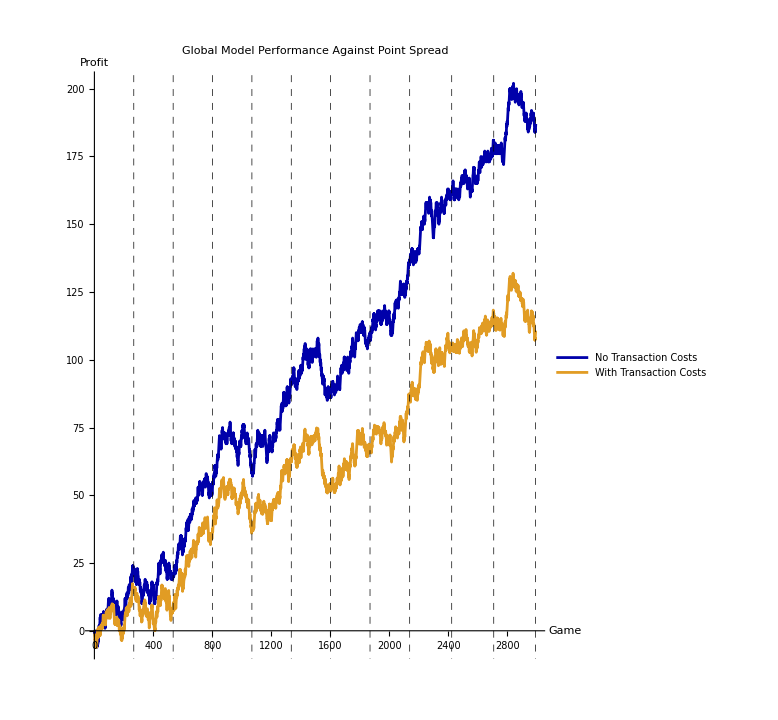

```mathematica
masseytrans = Import["/Users/totam/Downloads/Returns - masseyHodgeSpreadRes.csv"];
masseytranscum = masseytrans[[2;;Length[masseytrans],9]];

test2 = ListLinePlot[{original, masseytranscum}, ImageSize -> Large, PlotLabel -> "Global Model Performance Against Point Spread", PlotStyle -> {Darker[Blue], 15}, AxesLabel -> {"Game", "Profit"}, LabelStyle->Directive[Black, Bold], AxesStyle ->{{Black, Thick}, {Black, Thick}}, GridLines->{{267,534,801,1068,1335,1602,1869,2138,2423,2708,2992}}, GridLinesStyle->Directive[Black, Dashed], PlotLegends -> Placed[{"No Transaction Costs", "With Transaction Costs"}, {Center, Top}], AspectRatio->1.25]
Export["/Users/totam/Downloads/masseybaselineprofit.jpg",test2, ImageResolution -> 1200];
```

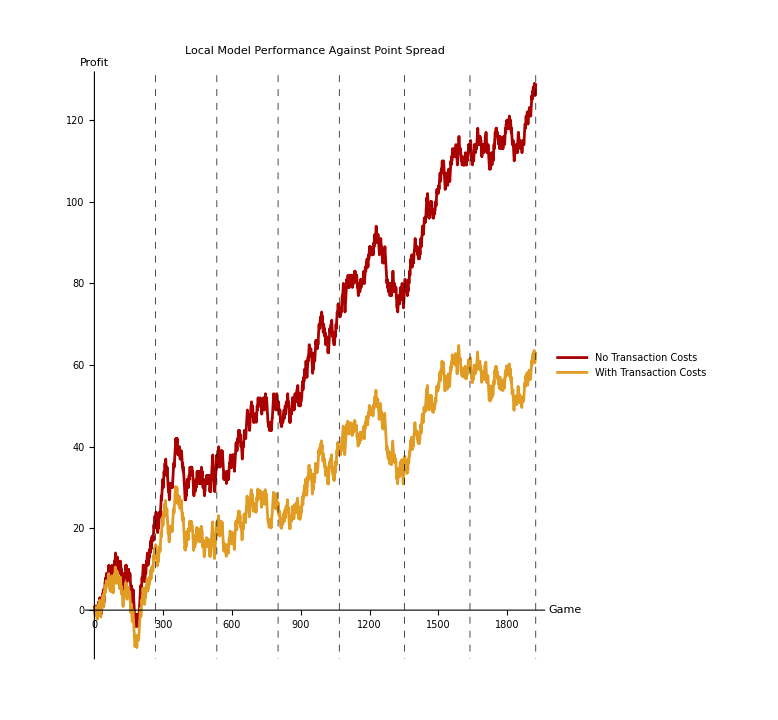

```mathematica
mldata = Import["/Users/totam/Downloads/Returns - holyShitRhinoEPA.csv"];
mldatafilter = mldata[[2;;Length[mldata],16]];
mltransactiondatafilter = mldata[[2;;Length[mldata],17]];
profitml = List[0];
profitmlcurr = 0;
Module[{i},
For[i = 1, i<= Length[mldatafilter], i++,
profitmlcurr = profitmlcurr+mldatafilter[[i]];
profitml = Append[profitml, profitmlcurr];
]
];

test3= ListLinePlot[{profitml, mltransactiondatafilter}, ImageSize -> Large, PlotLabel -> "Local Model Performance Against Point Spread", PlotStyle -> {Darker[Red], 15}, AxesLabel -> {"Game", "Profit"}, LabelStyle->Directive[Black, Bold], AxesStyle ->{{Black, Thick}, {Black, Thick}}, GridLines->{{267,534,801,1068,1353,1638,1925}}, GridLinesStyle->Directive[Black, Dashed], PlotLegends -> Placed[{"No Transaction Costs", "With Transaction Costs"}, {Center, Top}], AspectRatio->1.25]
Export["/Users/totam/Downloads/mlprofit.jpg",test3, ImageResolution -> 1200];
```

```mathematica
longspreads = Import["/Users/totam/Downloads/NFL Betting - spreadsClean.csv"];
spreads = longspreads[[2;;Length[longspreads], 4]];
years = longspreads[[2;;Length[longspreads],10]];
```

```mathematica
spreadyear = List[];
Module[{i},
For[i = 1, i<= Length[years], i++,
spreadyear = Append[spreadyear, {years[[i]], -1*spreads[[i]]}];
]
]
```

```mathematica
spreadHist = Histogram3D[spreadyear,{Length@data,Automatic}, ColorFunction->"SolarColors",PerformanceGoal->"Speed",Ticks->{20,20,20},ChartStyle->60,ViewPoint -> {Pi,Pi/3,2}, Boxed->False,FaceGrids->{Bottom,Front,Left},ImageSize->600, AxesLabel -> {"Season", "Point Spread", "Count"}, PlotLabel -> "Histogram of Vegas Point Spreads, 2002-2023", LabelStyle -> Directive[Bold, Black]]
Export["/Users/totam/Downloads/spreadHist.jpg",spreadHist, ImageResolution -> 1200];
```

-Graphics3D-

```mathematica
epadata= Import["/Users/totam/Downloads/QB Data - Shifted.csv"];
epa = epadata[[2;;Length[epadata], 5]];
epa = Select[epa, # != "NA"&];
```

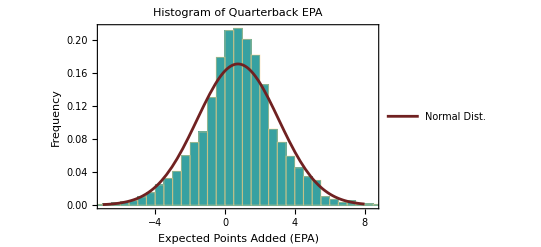

```mathematica
mu = 0.743518;
sigma = 2.33733;
epahist = Show[Histogram[epa,Automatic,"PDF",PlotLabel->"Histogram of Quarterback EPA", AxesLabel -> {"Expected Points Added (EPA)", "Frequency"},Frame->{True,True,False,False},FrameLabel->{"Expected Points Added (EPA)","Frequency"},ChartStyle->{Hue[0.5,0.66,0.63]},LabelStyle->{Bold, Black}],Plot[1/(sigma Sqrt[2 Pi]) Exp[-1/2 ((x-mu)/sigma)^2],{x,-7,8},PlotLegends->Placed[{"Normal Dist."}, {Right, Top}], PlotStyle->{Hue[0,0.71,0.44]},PlotLabel->"Histogram of Quarterback EPA"]]
Export["/Users/totam/Downloads/epaHist.jpg",epahist, ImageResolution -> 1200];
```

```mathematica
EstimatedDistribution[epa,NormalDistribution[mean,sigma]]
```

NormalDistribution[0.743518,2.33733]